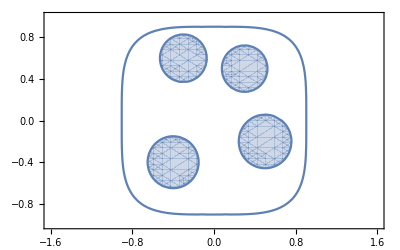

```mathematica
p = x^4+y^4-2/3;
c1 = (x+0.3)^2+(y-0.6)^2-1/19;
c2= (x+0.4)^2+(y+0.4)^2-1/16;
c3= (x-0.5)^2+(y+0.2)^2-1/15;
c4= (x-0.3)^2+(y-0.5)^2-1/20;
CP = ContourPlot[p==0,{x,-1.6,1.6},{y,-1,1}];
RP1 = RegionPlot[c1≤ 0,{x,-1.6,1.6},{y,-1,1}];
RP2 = RegionPlot[c2≤ 0,{x,-1.6,1.6},{y,-1,1}];
RP3 = RegionPlot[c3≤ 0,{x,-1.6,1.6},{y,-1,1}];
RP4 = RegionPlot[c4≤ 0,{x,-1.6,1.6},{y,-1,1}];
Show[RP1,RP2,RP3,RP4, CP,AspectRatio-> 1/1.6]
```

```mathematica
<<ToMatlab`
```

```mathematica
c4/.x-> "x_1"/.y-> "x_2"//ToMatlab//TextForm
```

(-1/20)+((-0.3E0)+x_1).^2+((-0.5E0)+x_2).^2;